# Computational Companion to “Quasi-Symmetric Nets: A Constructive Approach to the Equimodular Elliptic Type of Kokotsakis Polyhedra” — Example 1 Helper

## A. Nurmatov, M. Skopenkov, F. Rist, J. Klein, D. L. Michels Tested on: Mathematica 14.0

================= CONDITION (N.0) =================
✔ All vertices satisfy (N.0).

================= CONDITION (N.3) =================
✔ M1 = M2 = M3 = M4 = -1+√3

================= CONDITION (N.4) =================
✔ r1 = r2 = 2/(√3); ✔ r3 = r4 = 2/(√3)
✔ s1 = s4 = 3-√3; ✔ s2 = s3 = 1/(√3)

================= CONDITION (N.5) =================

⚠ Approximate validation using ε-tolerance. For rigorous proof, see the referenced paper.

✅ Valid Combination Found (M < 1):
e1 = -1, e2 = -1, e3 = 1
t1 = 0.K + 0.446521iK'
t2 = 1.K + 0.446521iK'
t3 = 3.K + 0.446521iK'
t4 = 0.K + 0.446521iK'
t1 + e1*t2 + e2*t3 + e3*t4 = -4.K + 0.iK'

================= OTHER PARAMETERS =================
u = 2-√3
σ1 = 165 °, σ2 = 165 °, σ3 = 195 °, σ4 = 165 °
f1 = 1/2 (1+√3), f2 = 4-2 √3, f3 = 4-2 √3, f4 = 1/2 (1+√3)
z1 = 1+√3, z2 = -1-2/(√3), z3 = -1-2/(√3), z4 = 1+√3
x1 = 3+2 √3, x2 = 3+2 √3, x3 = 3+2 √3, x4 = 3+2 √3
y1 = 2+√3, y2 = 1/(-1+1/(√3)), y3 = 1/(-1+1/(√3)), y4 = 2+√3
p1 = √(-1+2/(√3)), p2 = √(-1+2/(√3)), p3 = √(-1+2/(√3)), p4 = √(-1+2/(√3))
q1 = √(2-√3), q2 = ⅈ √(1-1/(√3)), q3 = ⅈ √(1-1/(√3)), q4 = √(2-√3)
p1·q1 = √(-4+7/(√3)), p2·q2 = ⅈ √(-5/3+√3), p3·q3 = ⅈ √(-5/3+√3), p4·q4 = √(-4+7/(√3))
OverBar[α1] = 60°, OverBar[β1] = 150°, OverBar[γ1] = 45°, OverBar[δ1] = 75°

================= Bricard's System of Equations =================
We introduce new notation for the cotangents of half of the dihedral angles. Denote w₁:= cot(θ_1/2), t:= cot(θ_2/2), w₂:= cot(θ_3/2), and z:= cot(θ_4/2)

P₁(w₁, z) = (w₁^2 ((3+√3) z^2+2 √3))/(4 √2)-((3+√3) w₁ z)/(2 √2)+(2 z^2+√3-1)/(4 √2) = 0

P₂(w₁, t) = 1/4 (-3 t^2-√3-1) w₁^2+1/4 (t^2+√3-1)-((√3-1) t w₁)/(√2) = 0

P₃(w₂, t) = 1/4 (3 t^2+√3+1) w₂^2+1/4 (-t^2-√3+1)-((√3-1) t w₂)/(√2) = 0

P₄(w₂, z) = (w₂^2 ((3+√3) z^2+2 √3))/(4 √2)-((3+√3) w₂ z)/(2 √2)+(2 z^2+√3-1)/(4 √2) = 0

================= FLEXIONS =================
Solutions to Bricard's equations under a free parameter t ∈ ℂ using Theorem 1:

Solution 1:

w₁(t) = (√(3 t^4+6 t^2+2)-√6 t+√2 t)/(3 t^2+√3+1)

t(t) = t

w₂(t) = (√(3 t^4+6 t^2+2)+√2 (√3-1) t)/(3 t^2+√3+1)

z(t) = (√(3 t^4+6 t^2+2))/(√3 t^2+√3+1)

Solution 2:

w₁(t) = -(√(3 t^4+6 t^2+2)+√2 (√3-1) t)/(3 t^2+√3+1)

t(t) = t

w₂(t) = -(√(3 t^4+6 t^2+2)-√6 t+√2 t)/(3 t^2+√3+1)

z(t) = -(√(3 t^4+6 t^2+2))/(√3 t^2+√3+1)

================= Equations: P₂(w₁, t) = 0 and P₃(w₂, t) = 0 =================
Let w₁ₛ₁ and w₁ₛ₂ be formulas for w₁(t) from solutions 1 and 2, respectively. Similarly, let w₂ₛ₁ and w₂ₛ₂ be the formulas for w₂(t). We show that all four pairs - (w₁ₛ₁, w₂ₛ₁), (w₁ₛ₁, w₂ₛ₂), (w₁ₛ₂, w₂ₛ₁), and (w₁ₛ₂, w₂ₛ₂) - solve equations P₂(w₁, t) = 0 and P₃(w₂, t) = 0.

Pair 1:

P₂(w₁ₛ₁, t) = 0  ✓

P₃(w₂ₛ₁, t) = 0  ✓

Pair 2:

P₂(w₁ₛ₁, t) = 0  ✓

P₃(w₂ₛ₂, t) = 0  ✓

Pair 3:

P₂(w₁ₛ₂, t) = 0  ✓

P₃(w₂ₛ₁, t) = 0  ✓

Pair 4:

P₂(w₁ₛ₂, t) = 0  ✓

P₃(w₂ₛ₂, t) = 0  ✓

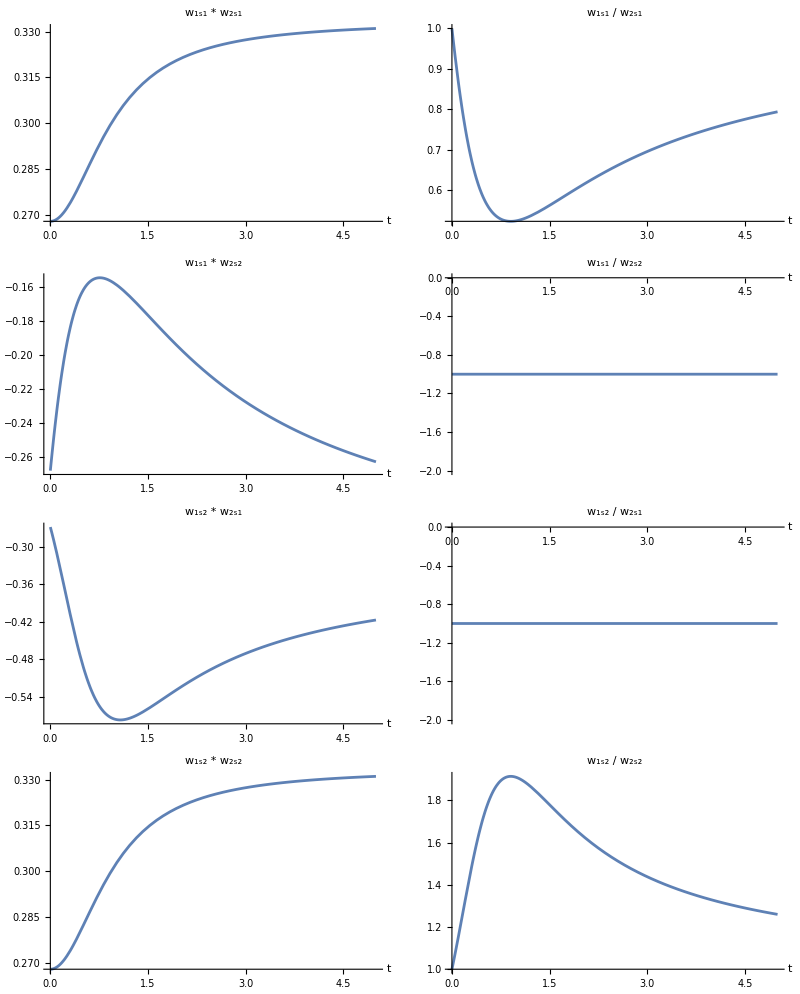
============= Plots of w₁(t)w₂(t) and w₁(t)/w₂(t) For All Pairs =============
Checking that all four pairs - (w₁ₛ₁, w₂ₛ₁), (w₁ₛ₁, w₂ₛ₂), (w₁ₛ₂, w₂ₛ₁), and (w₁ₛ₂, w₂ₛ₂) - does NOT satisfy w₁(t)/w₂(t) = c and w₁(t)w₂(t) = c when c ≠ -1.

-Graphics-

================= Equations: P₁(w₁, z) = 0 and P₄(w₂, z) = 0 =================
We solve P₁(w₁, z) = 0 and P₄(w₂, z) = 0 for w₁ and w₂.

w₁₁(z) = ((3+√3) z-√2 √(-((3+√3) z^4)+6 z^2+√3-3))/((3+√3) z^2+2 √3)
w₁₂(z) = (√2 √(-((3+√3) z^4)+6 z^2+√3-3)+(3+√3) z)/((3+√3) z^2+2 √3)

w₂₁(z) = ((3+√3) z-√2 √(-((3+√3) z^4)+6 z^2+√3-3))/((3+√3) z^2+2 √3)
w₂₂(z) = (√2 √(-((3+√3) z^4)+6 z^2+√3-3)+(3+√3) z)/((3+√3) z^2+2 √3)

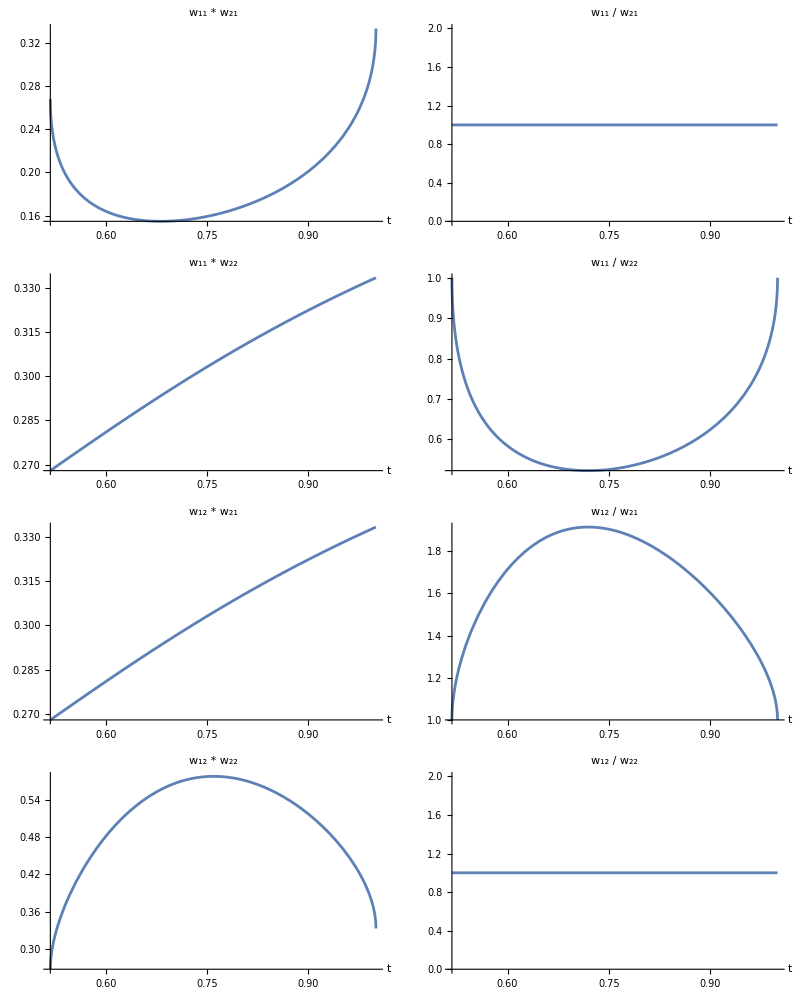
============= Plots of w₁(z)w₂(z) and w₁(z)/w₂(z) For All Pairs =============
Checking that all four pairs - (w₁₁(z), w₂₁(z)), (w₁₁(z), w₂₂(z)), (w₁₂(z), w₂₁(z)), and (w₁₂(z), w₂₂(z)) - does NOT satisfy w₁(z)/w₂(z) = c and w₁(z)w₂(z) = c when c ≠ +1.

-Graphics-

================= FLEXIBILITY (Double Checking) =================

Solution 1:

P_1(w₁, z) = 0

P_2(w₁, t) = 0

P_3(w₂, t) = 0

P_4(w₂, z) = 0

Solution 2:

P_1(w₁, z) = 0

P_2(w₁, t) = 0

P_3(w₂, t) = 0

P_4(w₂, z) = 0

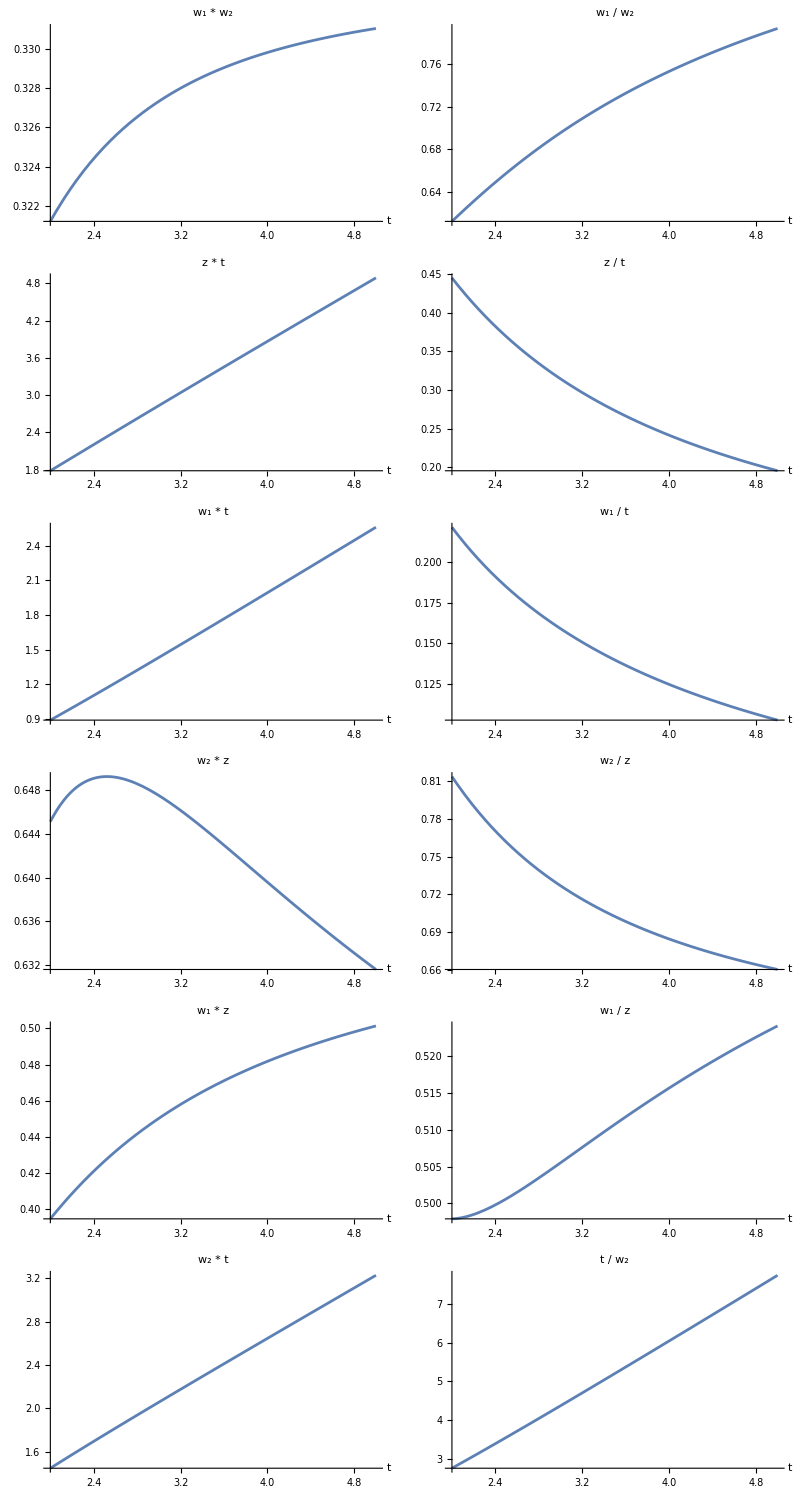
============= NOT LINEAR COMPOUND =============
Above we consider the first pair of equations (P₂(w₁, t) = 0 and P₃(w₂, t) = 0). Solving them as quadratic equations in w₁ and w₂, respectively we parametrize the solutions by the first three expressions in Solutions 1 and 2 in a neighborhood of any point (w₁, t, w₂) such that 2 + 6t.b2 + 3t⁴ ≠ 0. Here, we choose any continuous branch of the square root in this neighborhood, and the signs in ± need Not agree (this means we consider all 4 pairs we describe above). We conclude that one component of the solution set of the first pair of Bricard's equations satisfies w₁/w₂=-1, and NO other component satisfies w₁/w₂=const NOR w₁w₂=const.

Analogously, one component of the solution set of the other pair of equations (P₁(w₁, z) = 0 and P₄(w₂, z) = 0) satisfies w₁/w₂=+1,, and NO other component satisfies w₁/w₂=const NOR w₁w₂=const. As a result, NO component of the solution set of all four equations satisfies w₁/w₂=const NOR w₁w₂=const. So, our example does not belong to the linear compound class, even after switching the
boundary strips.

Below, we also present the plots of functions w₁w₂, w₁/w₂, zt, z/t, w₁t, w₁/t, w₂z, w₂/z, w₁z, w₁/z, w₂t, and t/w₂.

Solution 1:

-Graphics-

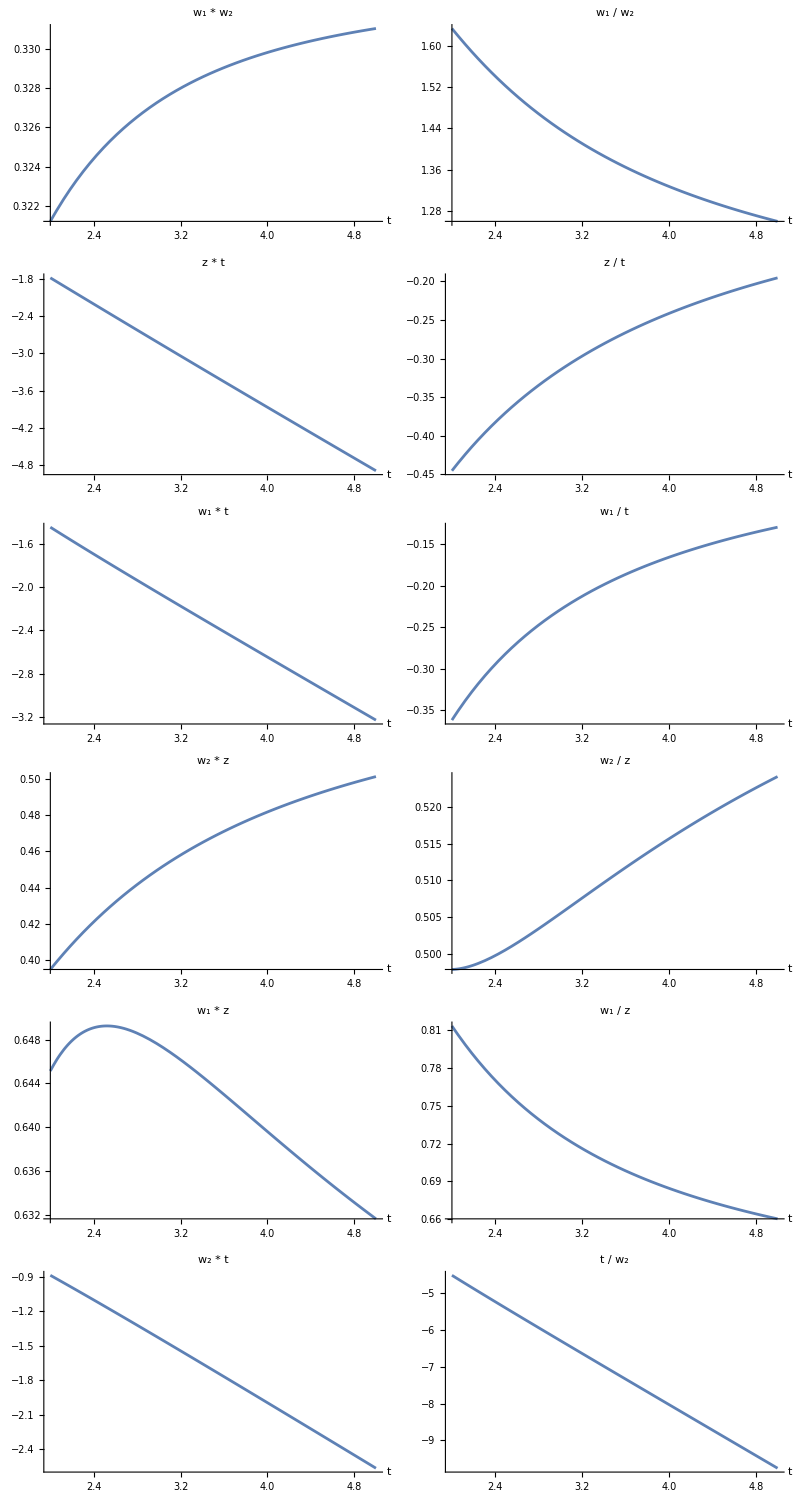
Solution 2:

-Graphics-

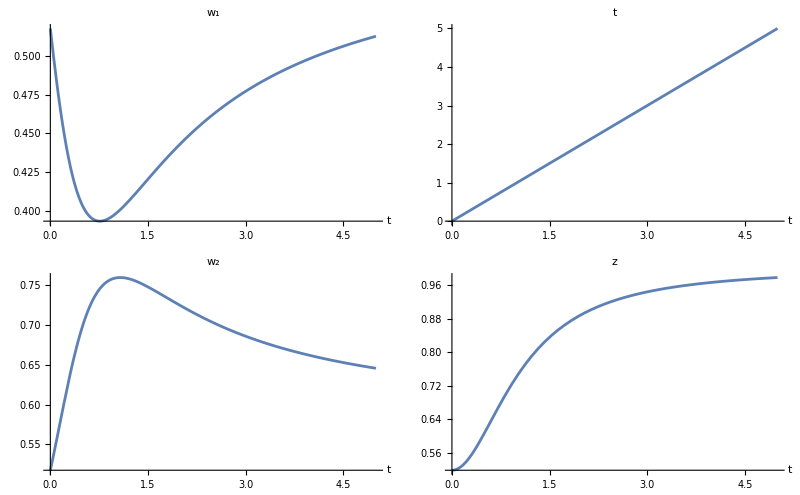
================= NOT TRIVIAL (FLEXION 1) =================
This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions w₁, t, w₂, or z is constant.

-Graphics-

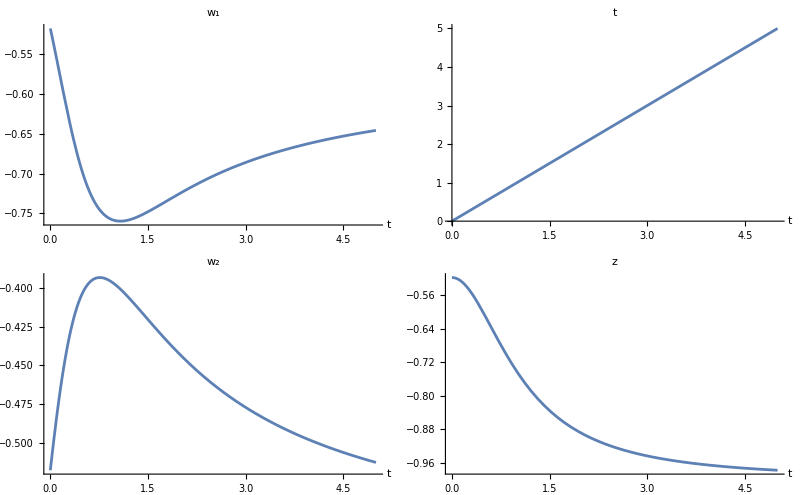
================= NOT TRIVIAL (FLEXION 2) =================
This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions w₁, t, w₂, or z is constant.

-Graphics-

================= NOT CONIC & NOT CHIMERA & NOT LINEAR CONJUGATE & NOT ISOGONAL=================
Condition (N.0) is satisfied for all i=1,...,4 ⇒ NOT equimodular-conic, NOT chimera, NOT isogonal and NOT linear conjugate. Applying any boundary-strip switch still preserves (N.0), so no conic, no chimera, no isogonal and no linear conjugate form emerges.

CONDITION (N.0) AFTER SWITCHING BOUNDARY STRIPS
Right: Condition (N.0) is still satisfied.
Left: Condition (N.0) is still satisfied.
Lower: Condition (N.0) is still satisfied.
Upper: Condition (N.0) is still satisfied.
Right + Left: Condition (N.0) is still satisfied.
Right + Lower: Condition (N.0) is still satisfied.
Right + Upper: Condition (N.0) is still satisfied.
Left + Lower: Condition (N.0) is still satisfied.
Left + Upper: Condition (N.0) is still satisfied.
Lower + Upper: Condition (N.0) is still satisfied.
Right + Left + Lower: Condition (N.0) is still satisfied.
Right + Left + Upper: Condition (N.0) is still satisfied.
Right + Lower + Upper: Condition (N.0) is still satisfied.
Left + Lower + Upper: Condition (N.0) is still satisfied.
Right + Left + Lower + Upper: Condition (N.0) is still satisfied.

================= ORTHOGONALITY CHECK =================
cos(αᵢ)·cos(γᵢ) ≠ cos(βᵢ)·cos(δᵢ) for at least one i = 1,..., 4 ⇒ NOT orthodiagonal. Switching boundary strips does not correct this.

Initial anglesDeg (no switches):

-> Condition met: At least one difference is non-zero.

NON-ORTHOGONALITY CHECK AFTER SWITCHING BOUNDARY STRIPS
Right: Condition met (at least one difference is non-zero).
Left: Condition met (at least one difference is non-zero).
Lower: Condition met (at least one difference is non-zero).
Upper: Condition met (at least one difference is non-zero).
Right + Left: Condition met (at least one difference is non-zero).
Right + Lower: Condition met (at least one difference is non-zero).
Right + Upper: Condition met (at least one difference is non-zero).
Left + Lower: Condition met (at least one difference is non-zero).
Left + Upper: Condition met (at least one difference is non-zero).
Lower + Upper: Condition met (at least one difference is non-zero).
Right + Left + Lower: Condition met (at least one difference is non-zero).
Right + Left + Upper: Condition met (at least one difference is non-zero).
Right + Lower + Upper: Condition met (at least one difference is non-zero).
Left + Lower + Upper: Condition met (at least one difference is non-zero).
Right + Left + Lower + Upper: Condition met (at least one difference is non-zero).

================= CONJUGATE-MODULAR CHECK =================
M1 = M2 = M3 = M4 = M and M ≠ 2 ⇒ NOT conjugate-modular. Boundary-strip switches preserve this.

Initial anglesDeg (no switches):

-> Condition met: All Mᵢ are equal and M ≠ 2.

CONJUGATE-MODULAR CHECK AFTER SWITCHING BOUNDARY STRIPS
Right: Condition met (All Mᵢ are equal and M ≠ 2).
Left: Condition met (All Mᵢ are equal and M ≠ 2).
Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Left + Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Left + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left + Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Left + Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left + Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).

```mathematica
(*================================================================================*)
(*================================================================================*)
(*================================================================================*)
(*Quit*)
(*All angle sets in degrees*)
alpha1 = 105;
beta1 =15;
gamma1 =120;
delta1 = 90;

sigma1 = (alpha1 + beta1 + gamma1 + delta1)/2;

anglesDeg={
{alpha1,beta1,gamma1, delta1},(*Vertex 1*)
{delta1,gamma1,beta1,alpha1},(*Vertex 2*)
{180 - delta1,180 - gamma1,180 - beta1,180 - alpha1},(*Vertex 3*)
{alpha1,beta1,gamma1, delta1}  (*Vertex 4*)};

(*-------------------------------------------*)
(*Function to compute sigma from 4 angles*)
computeSigma[{α_,β_,γ_,δ_}]:=(α+β+γ+δ)/2;

(*-------------------------------------------*)
(*Function to compute a,b,c,d from angles*)
computeABCD[{α_,β_,γ_,δ_}]:=Module[{alpha=α Degree,beta=β Degree,gamma=γ Degree,delta=δ Degree,sigma},sigma=computeSigma[{α,β,γ,δ} Degree];
{Sin[alpha]/Sin[sigma-alpha],Sin[beta]/Sin[sigma-beta],Sin[gamma]/Sin[sigma-gamma],Sin[delta]/Sin[sigma-delta]}];

(*-------------------------------------------*)
(*Compute all σ values*)
sigmas=computeSigma/@anglesDeg;

(*Compute all {a,b,c,d} values*)
results=computeABCD/@anglesDeg;

(*Optional:extract individual values*)
{a1,b1,c1,d1}=results[[1]];
{a2,b2,c2,d2}=results[[2]];
{a3,b3,c3,d3}=results[[3]];
{a4,b4,c4,d4}=results[[4]];
{σ1,σ2,σ3,σ4}=sigmas;


(*================================================================================*)
(*================================CONDITION (N.0)=================================*)
(*================================================================================*)
uniqueCombos={{1,1,1,1},{1,1,1,-1},{1,1,-1,-1},{1,1,-1,1},{1,-1,1,1},{1,-1,-1,1},{1,-1,1,-1},{1,-1,-1,-1}};

checkConditionN0Degrees[{α_,β_,γ_,δ_}]:=Module[{angles={α,β,γ,δ},results},results=Mod[uniqueCombos.angles,360]//Chop;
!MemberQ[results,0]];

conditionsN0=checkConditionN0Degrees/@anglesDeg;
allVerticesPass=And@@conditionsN0;

Column[{TextCell[Style["================= CONDITION (N.0) =================",Darker[Green],Bold, 16],"Text"],
If[allVerticesPass,
Style["✔ All vertices satisfy (N.0).",Darker[Green],Bold],Style["✘ Some vertices fail (N.0).",Red,Bold]]}]


(*================================================================================*)
(*================================CONDITION (N.3)=================================*)
(*================================================================================*)
Ms=FullSimplify[Times@@@results];
allEqualQ=Simplify[Equal@@Ms];

Column[{TextCell[Style["================= CONDITION (N.3) =================",Blue,Bold, 16],"Text"],If[allEqualQ,
Row[{Style["✔ M1 = M2 = M3 = M4 = ",Bold],Ms[[1]]}],Style["✘ M_i are not all equal.",Red,Bold]]}]


(*================================================================================*)
(*===========================CONDITION (N.4)===========================*)
(*================================================================================*)
aList=results[[All,1]];
cList=results[[All,3]];
dList=results[[All,4]];

rList=FullSimplify/@(aList*dList);{r1,r2,r3,r4}=rList;
sList=FullSimplify/@(cList*dList);{s1,s2,s3,s4}=sList;

Column[{TextCell[Style["================= CONDITION (N.4) =================",Darker[Blue],Bold, 16],"Text"],If[r1==r2&&r3==r4&&s1==s4&&s2==s3,Column[{Row[{Style["✔ r1 = r2 = ",Bold],r1, Style["; ✔ r3 = r4 = ",Bold],r3}],Row[{Style["✔ s1 = s4 = ",Bold],s1, Style["; ✔ s2 = s3 = ",Bold],s2}]}],Style["✘ Condition (N.4) fails.",Red,Bold]]
}]


(*================================================================================*)
(*=================================CONDITION (N.5)===============================*)
(*================================================================================*)
fList=FullSimplify/@(aList*cList);{f1,f2,f3,f4}=fList;
M1=Ms[[1]];

m[M1_]:=Piecewise[{{1-M1,M1<1},{(M1-1)/M1,M1>1}}]//N;
K=EllipticK[m[M1]]//N;
Kp=EllipticK[1-m[M1]]//N;

computeTi[i_]:=Module[{sigma=sigmas[[i]],r=rList[[i]],s=sList[[i]],f=fList[[i]],base},base=I*Im[InverseJacobiDN[Piecewise[{{Sqrt[f],M1<1},{1/Sqrt[f],M1>1}}],m[M1]]] / Kp;
Which[sigma<180,Which[r>1&&s>1,base,(r<1&&s>1)||(r>1&&s<1),1+base,r<1&&s<1,2+base],sigma>180,Which[r>1&&s>1,2+base,(r<1&&s>1)||(r>1&&s<1),3+base,r<1&&s<1,base]]];

tList=computeTi/@Range[4];
RoundWithTolerance[x_,tol_:10^-6]:=Module[{nearest},nearest=Round[x];
If[Abs[x-nearest]<=tol,nearest,x]];

checkValidCombination[M1_,ε_:10^-6]:=Module[{i,combo,dotProd,rePart,imPart,n2,expr,foundQ=False},Print[Style["⚠ Approximate validation using ε-tolerance. For rigorous proof, see the referenced paper.",Darker@Orange,Italic]];
Do[combo=uniqueCombos[[i]];
dotProd=tList.combo;
rePart=Abs[Re[dotProd]];
imPart=Abs[Im[dotProd]];
If[M1<1,
If[Mod[RoundWithTolerance[rePart], 4]<ε,
If[Mod[RoundWithTolerance[imPart], 2]<ε,expr=tList[[1]]+combo[[2]] tList[[2]]+combo[[3]] tList[[3]]+combo[[4]] tList[[4]];
Print[Style["✅ Valid Combination Found (M < 1):",Darker[Green],Bold],"\n",Style["e1 = ", Bold],combo[[2]],Style[", e2 = ", Bold],combo[[3]],Style[", e3 = ", Bold],combo[[4]],"\n",Style["t1 = ", Bold],Re[tList[[1]]],"K + ",Im[tList[[1]]],"iK'","\n",Style["t2 = ", Bold],Re[tList[[2]]],"K + ",Im[tList[[2]]],"iK'","\n",Style["t3 = ", Bold],Re[tList[[3]]],"K + ",Im[tList[[3]]],"iK'","\n",Style["t4 = ", Bold],Re[tList[[4]]],"K + ",Im[tList[[4]]],"iK'","\n",Style["t1 + e1*t2 + e2*t3 + e3*t4 = ", Bold],Re[expr],"K + ",Im[expr],"iK'"];
foundQ=True;
Break[]]]];
If[M1>1,
If[Mod[RoundWithTolerance[imPart], 2]<ε, n2=Quotient[RoundWithTolerance[imPart], 2];
If[Mod[RoundWithTolerance[Abs[rePart-2 n2]], 4]<ε,expr=tList[[1]]+combo[[2]] tList[[2]]+combo[[3]] tList[[3]]+combo[[4]] tList[[4]];
Print[Style["✅ Valid Combination Found (M > 1):",Darker[Green],Bold],"\n",Style["e1 = ", Bold],combo[[2]],Style[", e2 = ", Bold],combo[[3]],Style[", e3 = ", Bold],combo[[4]],"\n",Style["t1 = ", Bold],Re[tList[[1]]],"K + ",Im[tList[[1]]],"iK'","\n",Style["t2 = ", Bold],Re[tList[[2]]],"K + ",Im[tList[[2]]],"iK'","\n",Style["t3 = ", Bold],Re[tList[[3]]],"K + ",Im[tList[[3]]],"iK'","\n",Style["t4 = ", Bold],Re[tList[[4]]],"K + ",Im[tList[[4]]],"iK'","\n",Style["t1 + e1*t2 + e2*t3 + e3*t4 = ", Bold],Re[expr],"K + ",Im[expr],"iK'"];
foundQ=True;
Break[]]]],{i,Length[uniqueCombos]}];
If[!foundQ,Print[Style["❌ No valid combination found.",Red,Bold],"\n",Style["t1 = ", Bold],Re[tList[[1]]],"K + ",Im[tList[[1]]],"iK'","\n",Style["t2 = ", Bold],Re[tList[[2]]],"K + ",Im[tList[[2]]],"iK'","\n",Style["t3 = ", Bold],Re[tList[[3]]],"K + ",Im[tList[[3]]],"iK'","\n",Style["t4 = ", Bold],Re[tList[[4]]],"K + ",Im[tList[[4]]],"iK'","\n"]];];


Column[{TextCell[Style["================= CONDITION (N.5) =================",Purple,Bold, 16],"Text"]}]
res=checkValidCombination[M1];


(*================================================================================*)
(*================================OTHER PARAMETER=================================*)
(*================================================================================*)
Column[{TextCell[Style["================= OTHER PARAMETERS =================",Darker[Purple],Bold,16],"Text"],
Row[{Style["u = ", Bold], 1 - M1}], Row[{Style["σ1 = ", Bold],σ1 Degree,Style[", σ2 = ", Bold],σ2 Degree,Style[", σ3 = ", Bold],σ3 Degree,Style[", σ4 = ", Bold],σ4 Degree}],
Row[{Style["f1 = ", Bold],f1,Style[", f2 = ", Bold],f2,Style[", f3 = ", Bold],f3,Style[", f4 = ", Bold],f4}],Row[{Style["z1 = ", Bold],FullSimplify[1/(f1-1)],Style[", z2 = ", Bold],FullSimplify[1/(f2-1)],Style[", z3 = ", Bold],FullSimplify[1/(f3-1)],Style[", z4 = ", Bold],FullSimplify[1/(f4-1)]}],Row[{Style["x1 = ", Bold],FullSimplify[1/(r1-1)],Style[", x2 = ", Bold],FullSimplify[1/(r2-1)],Style[", x3 = ", Bold],FullSimplify[1/(r3-1)],Style[", x4 = ", Bold],FullSimplify[1/(r4-1)]}],Row[{Style["y1 = ", Bold],FullSimplify[1/(s1-1)],Style[", y2 = ", Bold],FullSimplify[1/(s2-1)],Style[", y3 = ", Bold],FullSimplify[1/(s3-1)],Style[", y4 = ", Bold],FullSimplify[1/(s4-1)]}],
Row[{Style["p1 = ", Bold],Simplify[Sqrt[r1-1]],Style[", p2 = ", Bold],Simplify[Sqrt[r2-1]],Style[", p3 = ", Bold],Simplify[Sqrt[r3-1]],Style[", p4 = ", Bold],Simplify[Sqrt[r4-1]]}],
Row[{Style["q1 = ", Bold],Simplify[Sqrt[s1-1]],Style[", q2 = ", Bold],Simplify[Sqrt[s2-1]],Style[", q3 = ", Bold],Simplify[Sqrt[s3-1]],Style[", q4 = ", Bold],Simplify[Sqrt[s4-1]]}], 
Row[{Style["p1·q1 = ", Bold],Simplify[Sqrt[r1-1] Sqrt[s1-1]],Style[", p2·q2 = ", Bold],Simplify[Sqrt[r2-1] Sqrt[s2-1]],Style[", p3·q3 = ", Bold],Simplify[Sqrt[r3-1] Sqrt[s3-1]],Style[", p4·q4 = ", Bold],Simplify[Sqrt[r4-1] Sqrt[s4-1]]}],
Row[{Style["\!\(\*OverscriptBox[\(α1\), \(_\)]\) = ",Bold],σ1-anglesDeg[[1,1]],"°",Style[", \!\(\*OverscriptBox[\(β1\), \(_\)]\) = ",Bold],σ1-anglesDeg[[1,2]],"°",Style[", \!\(\*OverscriptBox[\(γ1\), \(_\)]\) = ",Bold],σ1-anglesDeg[[1, 3]],"°",Style[", \!\(\*OverscriptBox[\(δ1\), \(_\)]\) = ",Bold],σ1-anglesDeg[[1,4]],"°"}]
}]


(*================================================================================*)
(*==============================BRICARD's EQUATIONS==============================*)
(*================================================================================*)

(*Bricard's equation as defined in terms of angles and variables*)
BricardsEquation[{α_,β_,γ_,δ_},σ_,x_,y_]:=Module[
{c22,c20,c02,c11,c00},
c22=Sin[σ-δ] Sin[σ-δ-β];
c20=Sin[σ-α] Sin[σ-α-β];
c02=Sin[σ-γ] Sin[σ-γ-β];
c11=-Sin[α] Sin[γ];
c00=Sin[σ] Sin[σ-β];
c22 x^2 y^2+c20 x^2+c02 y^2+2 c11 x y+c00
];


(*Step 1: Bricard's system of equations*)
Column[{(*Header*)TextCell[Style["================= Bricard's System of Equations =================",Red,Bold,16],"Text"],(*Explanatory note*)
Row[{TextCell[Style["We introduce new notation for the cotangents of half of the dihedral angles. Denote w₁:= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,1]/2]],TextCell[Style[", t:= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,2]/2]], TextCell[Style[", w₂:= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,3]/2]],
TextCell[Style[", and z:= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,4]/2]]
}], Spacer[12],
(*Traditional form results*)Row[{"P₁(w₁, z) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,w₁,z]], w₁]], " = 0"}],Spacer[6],
Row[{"P₂(w₁, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,w₁,t]], w₁]], " = 0"}],Spacer[6],
Row[{"P₃(w₂, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,w₂,t]],w₂]], " = 0"}],Spacer[6],
Row[{"P₄(w₂, z) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[4]] Degree,sigmas[[4]] Degree,w₂,z]],w₂]], " = 0"}]
}]

(*discriminant*)
Disc[t_] := (Sin[sigma1 Degree] Sin[(sigma1 - alpha1 - beta1) Degree] + t^2 Sin[(sigma1 - alpha1) Degree] Sin[(sigma1 - beta1) Degree]) (Sin[(sigma1 - gamma1) Degree] Sin[(sigma1 - delta1) Degree] + t^2 Sin[(sigma1 - beta1 - gamma1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);

(*==================================FLEXION 1==================================*)
e0 =1;
W2[t_]:= t;
Z[t_] :=( -t Sin[beta1 Degree] + e0 Sqrt[Disc[t]]) / (Sin[(sigma1 - delta1) Degree] Sin[(sigma1 - alpha1 - beta1) Degree] + t^2 Sin[(sigma1 - alpha1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);
U[t_] :=( t Sin[beta1 Degree] + e0 Sqrt[Disc[t]]) / (Sin[(sigma1 - delta1) Degree] Sin[(sigma1 - alpha1 - beta1) Degree] + t^2 Sin[(sigma1 - alpha1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);
W1[t_] := e0 Sqrt[Disc[t]]/ (Sin[(sigma1 - gamma1) Degree] Sin[(sigma1 - delta1) Degree] + t^2 Sin[(sigma1 - beta1 - gamma1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);

(*==================================FLEXION 2==================================*)
e00 =-1;
W22[t_]:= t;
Z2[t_] :=( -t Sin[beta1 Degree] + e00 Sqrt[Disc[t]]) / (Sin[(sigma1 - delta1) Degree] Sin[(sigma1 - alpha1 - beta1) Degree] + t^2 Sin[(sigma1 - alpha1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);
U2[t_] :=( t Sin[beta1 Degree] + e00 Sqrt[Disc[t]]) / (Sin[(sigma1 - delta1) Degree] Sin[(sigma1 - alpha1 - beta1) Degree] + t^2 Sin[(sigma1 - alpha1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);
W12[t_] := e00 Sqrt[Disc[t]]/ (Sin[(sigma1 - gamma1) Degree] Sin[(sigma1 - delta1) Degree] + t^2 Sin[(sigma1 - beta1 - gamma1) Degree] Sin[(sigma1 - beta1 - delta1) Degree]);


(*Step 2: Checking that formula from Theorem 1 simplifies to (E.1)*)
Column[{(*Header*)TextCell[Style["================= FLEXIONS =================",Darker[Red],Bold,16],"Text"],(*Explanatory note*)TextCell[Style["Solutions to Bricard's equations under a free parameter t ∈ ℂ using Theorem 1:",GrayLevel[0.3],13],"Text"],Spacer[12],
(*Heading for results*)TextCell[Style["Solution 1:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"w₁(t) = ",TraditionalForm[FullSimplify[Z[t]]]}],Spacer[6],
Row[{"t(t) = ",TraditionalForm[FullSimplify[W2[t]]]}],Spacer[6],
Row[{"w₂(t) = ",TraditionalForm[FullSimplify[U[t]]]}],Spacer[6],
Row[{"z(t) = ",TraditionalForm[FullSimplify[W1[t]]]}],  Spacer[12],
(*Heading for results*)TextCell[Style["Solution 2:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"w₁(t) = ",TraditionalForm[FullSimplify[Z2[t]]]}],Spacer[6],
Row[{"t(t) = ",TraditionalForm[FullSimplify[W22[t]]]}],Spacer[6],
Row[{"w₂(t) = ",TraditionalForm[FullSimplify[U2[t]]]}],Spacer[6],
Row[{"z(t) = ",TraditionalForm[FullSimplify[W12[t]]]}]
}]


(*Step 3: Checking that (E.1) solves P₂(w₁, t) = 0 and P₃(w₂, t) = 0 even when +- signs do NOT agree*)
Column[{(*Header*)TextCell[Style["================= Equations: P₂(w₁, t) = 0 and P₃(w₂, t) = 0 =================",Orange,Bold,16],"Text"],(*Explanatory note*)TextCell[Style["Let w₁ₛ₁ and w₁ₛ₂ be formulas for w₁(t) from solutions 1 and 2, respectively. Similarly, let w₂ₛ₁ and w₂ₛ₂ be the formulas for w₂(t). We show that all four pairs - (w₁ₛ₁, w₂ₛ₁), (w₁ₛ₁, w₂ₛ₂), (w₁ₛ₂, w₂ₛ₁), and (w₁ₛ₂, w₂ₛ₂) - solve equations P₂(w₁, t) = 0 and P₃(w₂, t) = 0.",GrayLevel[0.3],13],"Text"],Spacer[12],
(*Heading for results*)TextCell[Style["Pair 1:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₂(w₁ₛ₁, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],t]], w₁]], "  ",Style["✓",Darker[Green],Bold]}],Spacer[6],
Row[{"P₃(w₂ₛ₁, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,U[t],t]],w₂]],"  ",Style["✓",Darker[Green],Bold]}],Spacer[12],

TextCell[Style["Pair 2:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₂(w₁ₛ₁, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],t]], w₁]], "  ",Style["✓",Darker[Green],Bold]}],Spacer[6],
Row[{"P₃(w₂ₛ₂, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,U2[t],t]],w₂]],"  ",Style["✓",Darker[Green],Bold]}],Spacer[12],

TextCell[Style["Pair 3:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₂(w₁ₛ₂, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z2[t],t]], w₁]], "  ",Style["✓",Darker[Green],Bold]}],Spacer[6],
Row[{"P₃(w₂ₛ₁, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,U[t],t]],w₂]],"  ",Style["✓",Darker[Green],Bold]}],Spacer[12],

TextCell[Style["Pair 4:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₂(w₁ₛ₂, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z2[t],t]], w₁]], "  ",Style["✓",Darker[Green],Bold]}],Spacer[6],
Row[{"P₃(w₂ₛ₂, t) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,U2[t],t]],w₂]],"  ",Style["✓",Darker[Green],Bold]}]
}]

(*Step 4: Checking that (E.1) does NOT satisfy w₁(t)/w₂(t) = c and w₁(t)w₂(t) = c when c is less or greater -1 even when +- signs do NOT agree*)
tMin=0;
tMax=5;

expressions={Z[t] * U[t],Z[t]/U[t], Z[t]*U2[t],Z[t]/U2[t],Z2[t] * U[t],Z2[t]/U[t], Z2[t] * U2[t],Z2[t]/U2[t]};
labels={"w₁ₛ₁ * w₂ₛ₁","w₁ₛ₁ / w₂ₛ₁","w₁ₛ₁ * w₂ₛ₂","w₁ₛ₁ / w₂ₛ₂",  "w₁ₛ₂ * w₂ₛ₁","w₁ₛ₂ / w₂ₛ₁", "w₁ₛ₂ * w₂ₛ₂","w₁ₛ₂ / w₂ₛ₂"}; 
Column[{TextCell[Style["============= Plots of w₁(t)w₂(t) and w₁(t)/w₂(t) For All Pairs =============",Darker[Orange],Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["Checking that all four pairs - (w₁ₛ₁, w₂ₛ₁), (w₁ₛ₁, w₂ₛ₂), (w₁ₛ₂, w₂ₛ₁), and (w₁ₛ₂, w₂ₛ₂) - does NOT satisfy w₁(t)/w₂(t) = c and w₁(t)w₂(t) = c when c ≠ -1.",GrayLevel[0.3]],"Text"],
Spacer[12],

(*Plots panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]


(*Step 5: Solving P₁(w₁, z) = 0 and P₄(w₂, z) = 0 for w₁ and w₂*)
(*Define the first Bricard equation P1(Z,z)=0*)
P1=BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z,z];
(*Solve for Z1,Z2*)
solutionZExpressions=(Z/. FullSimplify[Solve[P1==0,Z]]);
Zz1[z_]:=solutionZExpressions[[1]];
Zz2[z_]:=solutionZExpressions[[2]];

(*Define the fourth Bricard equation P4(U,z)=0*)
P4=BricardsEquation[anglesDeg[[4]] Degree,sigmas[[4]] Degree,U,z];
(*Solve for U1,U2*)
solutionUExpressions=(U/. FullSimplify[Solve[P4==0,U]]);
Uu1[z_]:=solutionUExpressions[[1]];
Uu2[z_]:=solutionUExpressions[[2]];

Column[{(*Header*)TextCell[Style["================= Equations: P₁(w₁, z) = 0 and P₄(w₂, z) = 0 =================",Darker[Cyan],Bold,16],"Text"],(*Explanatory note*)TextCell[Style["We solve P₁(w₁, z) = 0 and P₄(w₂, z) = 0 for w₁ and w₂.",GrayLevel[0.3],13],"Text"],Spacer[12],
(*Heading for results*)Row[{"w₁₁(z) = ",TraditionalForm[Zz1[z]]}],Row[{"w₁₂(z) = ",TraditionalForm[Zz2[z]]}],Spacer[6],Row[{"w₂₁(z) = ",TraditionalForm[Uu1[z]]}],Row[{"w₂₂(z) = ",TraditionalForm[Uu2[z]]}]
}]

(*Step 6: Checking that pairs (w₁₁(z), w₂₁(z)), (w₁₁(z), w₂₂(z)), (w₁₂(z), w₂₁(z)), and (w₁₂(z), w₂₂(z)) does NOT satisfy w₁(z)/w₂(z) = c and w₁(z)w₂(z) = c when c is less or greater 1*)
zMin=Sqrt[(3-Sqrt[3]) / (3+Sqrt[3])];
zMax=1;

expressions={Zz1[z] * Uu1[z],Zz1[z]/Uu1[z], Zz1[z]*Uu2[z],Zz1[z]/Uu2[z],Zz2[z] * Uu1[z],Zz2[z]/Uu1[z], Zz2[z] * Uu2[z],Zz2[z]/Uu2[z]};
labels={"w₁₁ * w₂₁","w₁₁ / w₂₁","w₁₁ * w₂₂","w₁₁ / w₂₂",  "w₁₂ * w₂₁","w₁₂ / w₂₁", "w₁₂ * w₂₂","w₁₂ / w₂₂"}; 
Column[{TextCell[Style["============= Plots of w₁(z)w₂(z) and w₁(z)/w₂(z) For All Pairs =============",Magenta,Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["Checking that all four pairs - (w₁₁(z), w₂₁(z)), (w₁₁(z), w₂₂(z)), (w₁₂(z), w₂₁(z)), and (w₁₂(z), w₂₂(z)) - does NOT satisfy w₁(z)/w₂(z) = c and w₁(z)w₂(z) = c when c ≠ +1.",GrayLevel[0.3]],"Text"],
Spacer[12],

(*Plots panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{z,zMin,zMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]

(*Compute and print all P_i for flexion 1*)
TextCell[Style["================= FLEXIBILITY (Double Checking) =================",Darker[Magenta],Bold, 16],"Text"]
funcs={{w₁, z},{w₁, t},{w₂, t},{w₂, z}};
TextCell[Style["Solution 1:",Bold,14],"Text"]
Do[angles=anglesDeg[[i]] Degree;
sigma=sigmas[[i]] Degree;
{α,β,γ,δ}=angles;
poly=Which[i==1,BricardsEquation[{α,β,γ,δ},sigma,Z[t],W1[t]],i==2,BricardsEquation[{α,β,γ,δ},sigma,Z[t],W2[t]],i==3,BricardsEquation[{α,β,γ,δ},sigma,U[t],W2[t]],i==4,BricardsEquation[{α,β,γ,δ},sigma,U[t],W1[t]]];
Print[Row[{Subscript["P",i],"(",funcs[[i,1]],", ",funcs[[i,2]],") = ",FullSimplify[poly]}]],{i,1,4}];

(*Compute and print all P_i for flexion 2*)
TextCell[Style["Solution 2:",Bold,14],"Text"]
funcs={{w₁, z},{w₁, t},{w₂, t},{w₂, z}};
Do[angles=anglesDeg[[i]] Degree;
sigma=sigmas[[i]] Degree;
{α,β,γ,δ}=angles;
poly=Which[i==1,BricardsEquation[{α,β,γ,δ},sigma,Z2[t],W12[t]],i==2,BricardsEquation[{α,β,γ,δ},sigma,Z2[t],W22[t]],i==3,BricardsEquation[{α,β,γ,δ},sigma,U2[t],W22[t]],i==4,BricardsEquation[{α,β,γ,δ},sigma,U2[t],W12[t]]];
Print[Row[{Subscript["P",i],"(",funcs[[i,1]],", ",funcs[[i,2]],") = ",FullSimplify[poly]}]],{i,1,4}];


(*================================================================================*)
(*===================NOT LINEAR COMPOUND===================*)
(*================================================================================*)
(*Define domain limits for t*)
tMin=2;
tMax=5;
(*{TraditionalForm[cot[Subscript[θ,1]/2]],TraditionalForm[cot[Subscript[θ,2]/2]],TraditionalForm[cot[Subscript[θ,3]/2]],TraditionalForm[cot[Subscript[θ,4]/2]]};*)

(*==================================FLEXION 1==================================*)
(*List of expressions& labels*)
expressions={Z[t]*U[t],Z[t]/U[t],W1[t]*W2[t],W1[t]/W2[t],Z[t]*W2[t],Z[t]/W2[t],U[t]*W1[t],U[t]/W1[t],Z[t]*W1[t],Z[t]/W1[t],W2[t]*U[t],W2[t]/U[t]};
labels={"w₁ * w₂","w₁ / w₂","z * t","z / t","w₁ * t","w₁ / t","w₂ * z","w₂ / z","w₁ * z","w₁ / z","w₂ * t","t / w₂"};

Column[{TextCell[Style["============= NOT LINEAR COMPOUND =============",Darker[Brown],Bold,16],"Text"], 
(*Explanatory text*)TextCell[Style["Above we consider the first pair of equations (P₂(w₁, t) = 0 and P₃(w₂, t) = 0). Solving them as quadratic equations in w₁ and w₂, respectively we parametrize the solutions by the first three expressions in Solutions 1 and 2 in a neighborhood of any point (w₁, t, w₂) such that 2 + 6t.b2 + 3t⁴ ≠ 0. Here, we choose any continuous branch of the square root in this neighborhood, and the signs in ± need Not agree (this means we consider all 4 pairs we describe above). We conclude that one component of the solution set of the first pair of Bricard's equations satisfies w₁/w₂=-1, and NO other component satisfies w₁/w₂=const NOR w₁w₂=const.

Analogously, one component of the solution set of the other pair of equations (P₁(w₁, z) = 0 and P₄(w₂, z) = 0) satisfies w₁/w₂=+1,, and NO other component satisfies w₁/w₂=const NOR w₁w₂=const. As a result, NO component of the solution set of all four equations satisfies w₁/w₂=const NOR w₁w₂=const. So, our example does not belong to the linear compound class, even after switching the
boundary strips.",GrayLevel[0.3]],"Text"],
Spacer[6],
TextCell[Style["Below, we also present the plots of functions w₁w₂, w₁/w₂, zt, z/t, w₁t, w₁/t, w₂z, w₂/z, w₁z, w₁/z, w₂t, and t/w₂.",GrayLevel[0.3]],"Text"],
Spacer[6],
TextCell[Style["Solution 1:",Bold,14],"Text"],Spacer[12],
Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]


(*==================================FLEXION 2==================================*)
(*List of expressions& labels*)
expressions={Z2[t]*U2[t],Z2[t]/U2[t],W12[t]*W22[t],W12[t]/W22[t],Z2[t]*W22[t],Z2[t]/W22[t],U2[t]*W12[t],U2[t]/W12[t],Z2[t]*W12[t],Z2[t]/W12[t],W22[t]*U2[t],W22[t]/U2[t]};
labels={"w₁ * w₂","w₁ / w₂","z * t","z / t","w₁ * t","w₁ / t","w₂ * z","w₂ / z","w₁ * z","w₁ / z","w₂ * t","t / w₂"};

Column[{ TextCell[Style["Solution 2:",Bold,14],"Text"],Spacer[12],
(*Plots panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]


(*================================================================================*)
(*==================================NOT TRIVIAL==================================*)
(*================================================================================*)
(*Define domain limits for t*)
tMin=0;
tMax = 5;

(*==================================FLEXION 1==================================*)
(*List of expressions to plot*)
expressions={Z[t],W2[t],U[t], W1[t]};
labels={"w₁","t","w₂","z"};

Column[{TextCell[Style["================= NOT TRIVIAL (FLEXION 1) =================",Darker[Pink],Bold,16],"Text"], 
(*Explanatory text*)TextCell[Style["This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions w₁, t, w₂, or z is constant.",GrayLevel[0.3]],"Text"], 
Spacer[12],
(*Plots in a light panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]

}]

(*==================================FLEXION 2==================================*)
(*List of expressions to plot*)
expressions={Z2[t],W22[t],U2[t], W12[t]};
labels={"w₁","t","w₂","z"};

Column[{TextCell[Style["================= NOT TRIVIAL (FLEXION 2) =================",Darker[Green],Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions w₁, t, w₂, or z is constant.",GrayLevel[0.3]],"Text"], 
Spacer[12],

(*Plots in a light panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]

}]


(*================================================================================*)
(*===========================SWITCHING BOUNDARY STRIPS===========================*)
(*================================================================================*)
SwitchingRightBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={1,2},{1,3},{4,2},{4,3}*)
modified[[1,2]]=180-anglesDeg[[1,2]];(*β1*)
modified[[1,3]]=180-anglesDeg[[1,3]];(*γ1*)
modified[[4,2]]=180-anglesDeg[[4,2]];(*β4*)
modified[[4,3]]=180-anglesDeg[[4,3]];(*γ4*)
modified]

SwitchingLeftBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={2,2},{2,3},{3,2},{3,3}*)
modified[[2,2]]=180-anglesDeg[[2,2]];(*β2*)
modified[[2,3]]=180-anglesDeg[[2,3]];(*γ2*)
modified[[3,2]]=180-anglesDeg[[3,2]];(*β3*)
modified[[3,3]]=180-anglesDeg[[3,3]];(*γ3*)
modified]

SwitchingLowerBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={1,1},{1,2},{2,1},{2,2}*)
modified[[1,1]]=180-anglesDeg[[1,1]];(*α1*)
modified[[1,2]]=180-anglesDeg[[1,2]];(*β1*)
modified[[2,1]]=180-anglesDeg[[2,1]];(*α2*)
modified[[2,2]]=180-anglesDeg[[2,2]];(*β2*)
modified]

SwitchingUpperBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={3,1},{3,2},{4,1},{4,2}*)
modified[[3,1]]=180-anglesDeg[[3,1]];(*α3*)
modified[[3,2]]=180-anglesDeg[[3,2]];(*β3*)
modified[[4,1]]=180-anglesDeg[[4,1]];(*α4*)
modified[[4,2]]=180-anglesDeg[[4,2]];(*β4*)
modified]


(*================================================================================*)
(*===================================NOT CONIC & NOT CHIMERA & NOT LINEAR CONJUGATE & NOT ISOGONAL====================================*)
(*================================================================================*)
Column[{TextCell[Style["================= NOT CONIC & NOT CHIMERA & NOT LINEAR CONJUGATE & NOT ISOGONAL=================",Blue,Bold,16],"Text"], 
TextCell[Style["Condition (N.0) is satisfied for all i=1,...,4 ⇒ NOT equimodular-conic, NOT chimera, NOT isogonal and NOT linear conjugate. Applying any boundary-strip switch still preserves (N.0), so no conic, no chimera, no isogonal and no linear conjugate form emerges.",  GrayLevel[0.3]],"Text"]
}]

(*Now the exact same Module for checking all switch combinations…*)
Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
passQ=And@@(checkConditionN0Degrees/@switched);
(*Print the result after switching*)
(*Print["\nSwitch combination: ",name];
Print["Switched anglesDeg:"];
Print[MatrixForm[switched]];*)
{name,passQ}],{combo,combinations}];
(*Display results*)Column[Prepend[Table[Module[{comboName=res[[1]],passQ=res[[2]]},Row[{Style[comboName<>": ",Bold],
If[passQ,
Style["Condition (N.0) is still satisfied.",Darker[Green]],Style["Condition (N.0) fails.",Red,Bold]
]
}
]],{res,results}],TextCell[Style["CONDITION (N.0) AFTER SWITCHING BOUNDARY STRIPS",14],"Text"]]]]


(*================================================================================*)
(*===============================NOT ORTHODIAGONAL===============================*)
(*================================================================================*)

(*Column[{TextCell[Style["================= NOT ORTHODIAGONAL =================",Darker[Blue],Bold,16],"Text"], 
TextCell[Style["cos(αᵢ)·cos(γᵢ) ≠ cos(βᵢ)·cos(δᵢ) for each i = 1 ⇒ NOT orthodiagonal. Switching boundary strips does not correct this.",  GrayLevel[0.3]],"Text"]
}]

Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Helper function:compute and print difference only*)formatOrthodiagonalCheck[quad_List]:=Module[{vals},vals=Table[Module[{a,b,c,d,lhs,rhs,diff},{a,b,c,d}=quad[[i]];
lhs=FullSimplify[Cos[a Degree] Cos[c Degree]];
rhs=FullSimplify[Cos[b Degree] Cos[d Degree]];
diff=Chop[lhs-rhs];
Style[Row[{"cos(α"<>ToString[i]<>")·cos(γ"<>ToString[i]<>") - ","cos(β"<>ToString[i]<>")·cos(δ"<>ToString[i]<>") = ",NumberForm[diff,{5,3}]}],If[diff==0,Red,Black]]],{i,Length[quad]}];
Column[vals]];
(*Orthodiagonal check for anglesDeg before any switching*)
Print[TextCell[Style["\nInitial anglesDeg (no switches):",Bold]]];
Print[MatrixForm[angles]];
Print[TextCell[Style["Orthodiagonal check: cos(αᵢ)·cos(γᵢ) - cos(βᵢ)·cos(δᵢ) for i = 1..4",Italic]]];
Print[formatOrthodiagonalCheck[angles]];
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
passQ=And@@(checkConditionN0Degrees/@switched);
Print[Style["\nSwitch combination: ", Bold],name];
Print[Style["Switched anglesDeg:", Italic]];
Print[MatrixForm[switched]];
Print[TextCell[Style["Orthodiagonal check: cos(αᵢ)·cos(γᵢ) - cos(βᵢ)·cos(δᵢ) for i = 1..4",Italic]]];
Print[formatOrthodiagonalCheck[switched]];
{name,passQ}],{combo,combinations}];]*)


Column[{TextCell[Style["================= ORTHOGONALITY CHECK =================",Darker[Blue],Bold,16],"Text"],TextCell[Style["cos(αᵢ)·cos(γᵢ) ≠ cos(βᵢ)·cos(δᵢ) for at least one i = 1,..., 4 ⇒ NOT orthodiagonal. Switching boundary strips does not correct this.",GrayLevel[0.3]],"Text"]}]

(*Helper function:Returns True if at least one cosine product difference is non-zero.Returns False if all differences are zero.*)
isNotOrthodiagonal[quad_List]:=Or@@Table[Module[{a,b,c,d,diff},{a,b,c,d}=quad[[i]];
diff=Chop[Cos[a Degree] Cos[c Degree]-Cos[b Degree] Cos[d Degree]];
diff!=0],{i,Length[quad]}];

(*First,check the initial,unswitched angles*)
Print[TextCell[Style["\nInitial anglesDeg (no switches):",Bold]]];
If[isNotOrthodiagonal[anglesDeg],Print[Style[" -> Condition met: At least one difference is non-zero.",Darker@Green]],Print[Style[" -> Condition NOT met: All differences are zero.",Red]]];

(*Now,use your desired module to check all switch combinations*)
Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches and store in'results'*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
(* ***THIS IS THE KEY CHANGE****)(*Set passQ using our new helper function*)passQ=isNotOrthodiagonal[switched];
{name,passQ}],{combo,combinations}];
(*Display results in the specified column format*)Column[Prepend[Table[Module[{comboName=res[[1]],passQ=res[[2]]},Row[{Style[comboName<>": ",Bold],If[passQ,Style["Condition met (at least one difference is non-zero).",Darker[Green]],Style["Condition NOT met (all differences are zero).",Red,Bold]]}]],{res,results}],TextCell[Style["\nNON-ORTHOGONALITY CHECK AFTER SWITCHING BOUNDARY STRIPS",14],"Text"]]]]



(*================================================================================*)
(*=============================NOT CONJUGATE-MODULAR=============================*)
(*================================================================================*)
(*Column[{TextCell[Style["================= NOT CONJUGATE-MODULAR =================",Purple,Bold,16],"Text"], 
TextCell[Style["M1 = M2 = M3 = M4 = M and M ≠ 2 ⇒ NOT conjugate-modular. Boundary-strip switches preserve this.",GrayLevel[0.3]],"Text"]
}]
Ms=FullSimplify[Times@@@results];
allEqualQ=Simplify[Equal@@Ms];

Module[{angles=anglesDeg,switchers,combinations,results,computeConjugateModularInfo},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Computes Mᵢ and pᵢ and prints them,with classification*)computeConjugateModularInfo[quad_List]:=Module[{abcdList,Ms,summary},abcdList=computeABCD/@quad;
Ms=FullSimplify[Times@@@abcdList];
summary=If[Simplify[Equal@@Ms]&&Ms[[1]]=!=2,Style["M1 = M2 = M3 = M4 = M and M ≠ 2",Bold],Style["M1 = M2 = M3 = M4 = M and M = 2",Red,Bold]];
Column[{Style["Mᵢ values:",Bold],Row[{"M1 = ",Ms[[1]],", M2 = ",Ms[[2]],", M3 = ",Ms[[3]],", M4 = ",Ms[[4]]}],summary}]];
(*Original anglesDeg check*)
Print[TextCell[Style["\nInitial configuration (no switches applied):",Bold]]];
Print[MatrixForm[angles]];
Print[computeConjugateModularInfo[angles]];
(*Generate all switch combinations (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate each switched configuration*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
passQ=And@@(checkConditionN0Degrees/@switched);
Print[Style["\nSwitch combination: ", Bold],name];
Print[Style["Switched anglesDeg:", Italic]];
Print[MatrixForm[switched]];
Print[computeConjugateModularInfo[switched]];
{name,passQ}],{combo,combinations}];]*)


Column[{TextCell[Style["================= CONJUGATE-MODULAR CHECK =================",Purple,Bold,16],"Text"],TextCell[Style["M1 = M2 = M3 = M4 = M and M ≠ 2 ⇒ NOT conjugate-modular. Boundary-strip switches preserve this.",GrayLevel[0.3]],"Text"]}]

(*Helper Function:Returns True if all M_i values are equal AND their common value is not 2. Returns False otherwise.*)
isNotConjugateModular[quad_List]:=Module[{abcdList,Ms},abcdList=computeABCD/@quad;
Ms=FullSimplify[Times@@@abcdList];
(*The condition is met if they are all equal AND the value isn't 2*)Simplify[Equal@@Ms]&&(Ms[[1]]!=2)];

(*First,check the initial,unswitched angles*)
Print[TextCell[Style["\nInitial anglesDeg (no switches):",Bold]]];
If[isNotConjugateModular[anglesDeg],Print[Style[" -> Condition met: All Mᵢ are equal and M ≠ 2.",Darker@Green]],Print[Style[" -> Condition NOT met.",Red]]];

(*Now,use the clean module to check all switch combinations*)
Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches and store the result*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
(*Set passQ using our new helper function for this check*)passQ=isNotConjugateModular[switched];
{name,passQ}],{combo,combinations}];
(*Display results in the specified column format*)Column[Prepend[Table[Module[{comboName=res[[1]],passQ=res[[2]]},Row[{Style[comboName<>": ",Bold],If[passQ,Style["Condition met (All Mᵢ are equal and M ≠ 2).",Darker[Green]],Style["Condition NOT met.",Red,Bold]]}]],{res,results}],TextCell[Style["\nCONJUGATE-MODULAR CHECK AFTER SWITCHING BOUNDARY STRIPS",14],"Text"]]]]
```